```mathematica
TensorData = ToExpression[Import["C:\\ETH\\Neuro\\GlobalTracking\\GlobalTrackingScripts\\tensor_data.txt"]];
dim=Dimensions[TensorData]
Tensor[i_,j_,k_]:={{TensorData[[i,j,k,1]],TensorData[[i,j,k,2]],TensorData[[i,j,k,3]]},{TensorData[[i,j,k,2]],TensorData[[i,j,k,4]],TensorData[[i,j,k,5]]},{TensorData[[i,j,k,3]],TensorData[[i,j,k,5]],TensorData[[i,j,k,6]]}}
```

{9,9,9,6}

```mathematica
g[{ϕ_,θ_}]:={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}
angle[vec_]:={   Sign[vec[[2]]]ArcCos[vec[[1]]/Norm[{vec[[1]],vec[[2]]}]]   ,   ArcCos[vec[[3]] ]   }

SurfacePositions = Select[ Flatten[Table[{i,j,k},{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}],2], (#[[1]]==1 ||#[[1]]==dim[[1]] ||#[[2]]==1 ||#[[2]]==dim[[2]]||#[[3]]==1 ||#[[3]]==dim[[3]] )&];
```

### Initialization

```mathematica
Initialize[E0init_,αmaxinit_]:={

αmax = αmaxinit;
E0 =E0init;

Surface = Select[ Flatten[Table[{i,j,k,1},{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}],2], (#[[1]]==1 ||#[[1]]==dim[[1]] ||#[[2]]==1 ||#[[2]]==dim[[2]]||#[[3]]==1 ||#[[3]]==dim[[3]] )&];

S= Table[Eigenvectors[Tensor[i,j,k]][[1]],{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}];
(*S=Table[g[{RandomReal[{0,2Pi}],RandomReal[{0,Pi}]}],{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}];*)

A=Association[
Flatten[
Table[{i,j,k,1}->Association[{
"tensor"->Tensor[i,j,k],
"direction"->S[[i,j,k]],
"position" -> {i,j,k},
"neighbors"-> DeleteCases[
Flatten[
Table[{ii,jj,kk,1},
{ii,Max[1,i-1],Min[dim[[1]],i+1]},{jj,Max[1,j-1],Min[dim[[2]],j+1]},{kk,Max[1,k-1],Min[dim[[3]],k+1]}],
2],
{i,j,k,1}],
"forward"->{},
"backward"->{}}],
{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}],3]
];

AppendTo[A,
{}->Association[{
"tensor"->{},
"direction"->{},
"position" -> {},
"neighbors"-> {},
"forward"->{},
"backward"->{}}]
];
}
```

### Neighborhood Functions

```mathematica
F[spin_]:=Select[
A[spin]["neighbors"],
( (A[#]["position"]-A[spin]["position"]).A[spin]["direction"]>0  )&
]

B[spin_]:=Select[
A[spin]["neighbors"],
( (A[#]["position"]-A[spin]["position"]).A[spin]["direction"]<=0  )&
]
```

### Energy Functions

```mathematica
Eint[{}]:=0

Eint[spin_]:=Module[{COSα = {},backward,forward,connection},

forward = A[spin]["forward"];
backward = A[spin]["backward"];

If[backward≠{},
connection =A[backward]["position"]-A[spin]["position"];
AppendTo[COSα,Abs[connection.A[backward]["direction"]/Norm[connection]]];
AppendTo[COSα,Abs[connection.A[spin]["direction"]/Norm[connection]]];
];
If[forward≠{},
connection =A[forward]["position"]-A[spin]["position"];
AppendTo[COSα, Abs[connection.A[forward]["direction"] /Norm[connection]]];
AppendTo[COSα, Abs[connection.A[spin]["direction"]/Norm[connection] ]];
];

If[MemberQ[Surface,A[spin]["position"]],
E0/2. + Sum[-E0/4.-Log[If[(cosα-Cos[αmax])/(1-Cos[αmax])>0,(cosα-Cos[αmax])/(1-Cos[αmax]),10^-6]],{cosα,COSα}]
,
E0 + Sum[-E0/4.-Log[If[(cosα-Cos[αmax])/(1-Cos[αmax])>0,(cosα-Cos[αmax])/(1-Cos[αmax]),10^-6]],{cosα,COSα}]
]
]

Edata[spin_]:=A[spin]["direction"].Inverse[A[spin]["tensor"]].A[spin]["direction"]
```

### Create New Spin

```mathematica
CreateNew[str_,spin_]:=Module[{newposition,newforward,newbackward,newID},

If[str == "forward",

newposition = Round[A[spin]["position"]+A[spin]["direction"]];

If[1<=newposition[[1]]≤dim[[1]]&&1<=newposition[[2]]≤dim[[2]]&&1<=newposition[[3]]≤dim[[3]],

newID = Length[Select[A,#["position"]==newposition&]]+1;

AppendTo[A,
Append[newposition,newID]->Association[{
"tensor"->A[Append[newposition,newID-1]]["tensor"],
"direction"->A[spin]["direction"],
"position" -> newposition,
"neighbors"-> A[Append[newposition,newID-1]]["neighbors"],
"forward"->{},
"backward"->spin}]
];

newforward=Append[newposition,newID];
A[spin]["forward"] = newforward;

Table[AppendTo[A[n]["neighbors"],newforward],{n,A[newforward]["neighbors"]}];
If[MemberQ[SurfacePositions,newposition],AppendTo[Surface,newforward]];
,
Null;
]

,(*=======================================================*)

newposition = Round[A[spin]["position"]-A[spin]["direction"]];

If[1<=newposition[[1]]≤dim[[1]]&&1<=newposition[[2]]≤dim[[2]]&&1<=newposition[[3]]≤dim[[3]],

newID = Length[Select[A,#["position"]==newposition&]]+1;

AppendTo[A,
Append[newposition,newID]->Association[{
"tensor"->A[Append[newposition,newID-1]]["tensor"],
"direction"->A[spin]["direction"],
"position" -> newposition,
"neighbors"-> A[Append[newposition,newID-1]]["neighbors"],
"forward"->spin,
"backward"->{}}]
];

newbackward=Append[newposition,newID];
A[spin]["backward"] = newbackward;

Table[AppendTo[A[n]["neighbors"],newbackward],{n,A[newbackward]["neighbors"]}];
If[MemberQ[SurfacePositions,newposition],AppendTo[Surface,newbackward]];
,
Null;
]
]
]
```

### Associate Spin

```mathematica
Associate[spin_]:=Module[{oldforward,oldbackward,forwardneighbors,backwardneighbors,minforward={},minbackward={},E0,E1,ΔE,p},

forwardneighbors = F[spin];

ΔE =0.;
Table[
oldforward =A[spin]["forward"];
oldbackward=A[newforward]["backward"];

E0 = Eint[spin] +  Eint[oldforward] +
	Eint[newforward] + Eint[oldbackward];

A[oldforward]["backward"] = {};
A[oldbackward]["forward"] = {};
A[spin]["forward"] = newforward;
A[newforward]["backward"] = spin;

E1 = Eint[spin] +  Eint[newforward] +
	Eint[oldforward] + Eint[oldbackward];

If[E1-E0<=ΔE,

ΔE = E1-E0;
minforward = newforward;

A[oldforward]["backward"] = spin;
A[oldbackward]["forward"] = newforward;
A[spin]["forward"] = oldforward;
A[newforward]["backward"] = oldbackward;
,

A[oldforward]["backward"] = spin;
A[oldbackward]["forward"] = newforward;
A[spin]["forward"] = oldforward;
A[newforward]["backward"] = oldbackward;
]

,{newforward,forwardneighbors}];

p = Min[1., Exp[-ΔE]];

If[RandomReal[]< p && minforward ≠ {},

A[oldforward]["backward"] = {};
A[oldbackward]["forward"] = {};
A[spin]["forward"] = minforward;
A[minforward]["backward"] = spin;
,
CreateNew["forward",spin];
];

(*========================================*)

backwardneighbors = B[spin];

ΔE =0.;
Table[
oldforward =A[newbackward]["forward"];
oldbackward=A[spin]["backward"];

E0 = Eint[spin] +  Eint[oldforward] +
	Eint[newbackward] + Eint[oldbackward];

A[oldforward]["backward"] = {};
A[oldbackward]["forward"] = {};
A[spin]["backward"] = newbackward;
A[newbackward]["forward"] = spin;

E1 = Eint[spin] +  Eint[newbackward] +
	Eint[oldforward] + Eint[oldbackward];

If[E1-E0<=ΔE,

ΔE = E1-E0;
minbackward = newbackward;

A[oldforward]["backward"] = newbackward;
A[oldbackward]["forward"] = spin;
A[spin]["backward"] = oldbackward;
A[newbackward]["forward"] = oldforward;
,

A[oldforward]["backward"] = newbackward;
A[oldbackward]["forward"] = spin;
A[spin]["backward"] = oldbackward;
A[newbackward]["forward"] = oldforward;
]

,{newbackward,backwardneighbors}];

p = Min[1., Exp[-ΔE]];

If[RandomReal[]< p && minbackward ≠ {},
A[oldforward]["backward"] = {};
A[oldbackward]["forward"] = {};
A[spin]["backward"] = minbackward;
A[minbackward]["forward"] = spin;
,
CreateNew["backward",spin];
];
]
```

### Align Spin

```mathematica
Align[spin_]:=Module[{newdirection,olddirection,E0,E1,p},

olddirection=A[spin]["direction"];

newdirection =  olddirection + RandomReal[{-0.1,0.1},3];
newdirection=newdirection/Norm[newdirection];

E0 = Eint[spin] + Edata[spin];

A[spin]["direction"]=newdirection;

E1 = Eint[spin] + Edata[spin];

p = Min[1., Exp[E0-E1]];

If[RandomReal[]>p,
A[spin]["direction"]=olddirection;
]
]
```

### Testing

```mathematica
Energy ={};
Initialize[10^3.,Pi/3.];
Block[{i,j,k,n,s,N=3},

For[n=1,n≤N,n++,

Energy = Append[Energy,Sum[Eint[{i,j,k,1}]+Edata[{i,j,k,1}],{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}]];

For[i=2,i<dim[[1]],i++,
For[j=2,j<dim[[2]],j++,
For[k=2,k<dim[[3]],k++,
For[s=1,s≤Length[Select[A,#["position"] == {i,j,k}&]],s++,
Associate[{i,j,k,s}];
]]]]

For[i=1,i<=dim[[1]],i++,
For[j=1,j<=dim[[2]],j++,
For[k=1,k<=dim[[3]],k++,
For[s=1,s≤Length[Select[A,#["position"] == {i,j,k}&]],s++,
Align[{i,j,k,s}];
]]]]

Print[{n,Length[A]}];

];
]
```

{1,742}

{2,757}

{3,777}

```mathematica
EintDistr=Flatten[Table[Table[Eint[{i,j,k,s}],{s,1,Length[Select[A,#["position"] == {i,j,k}&]]}],{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}],3];
```

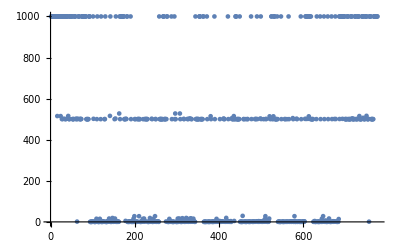

```mathematica
ListPlot[EintDistr]
```

```mathematica
EdataDistr=Flatten[Table[Table[Edata[{i,j,k,s}],{s,1,Length[Select[A,#["position"] == {i,j,k}&]]}],{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}],3];
```

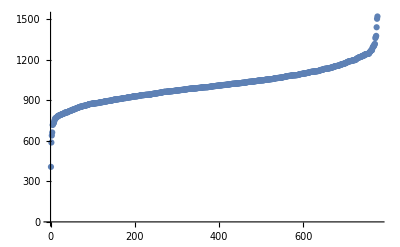

```mathematica
ListPlot[Sort[EdataDistr]]
```

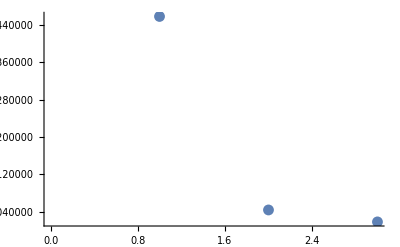

```mathematica
ListPlot[Energy,PlotRange->All]
```